TOV for Neutron stars. Equation of state: 
p = α ψ^γ
ρ = ψ + α/(γ-1)ψ^γ
The units are such that
4πG = c = ρ_*=1
Where ρ_* is the energy density equivalent of one neutron per square femtometers.

```mathematica
α=0.5;
```

```mathematica
γ=2;
```

```mathematica
Subscript[ψ, 0]=√2-1; (*This is the core psi parameter!*)
```

```mathematica
P[ψ_] = α*ψ^γ;
```

```mathematica
ρ[ψ_]=ψ + α/(γ-1)ψ^γ;
```

```mathematica
ϵ=0.0001;
```

```mathematica
L=5;
```

```mathematica
TOVeqs:=NDSolve[{α*γ*ψ[r]^(γ-1)*ψ'[r]+((ρ[ψ[r]] + P[ψ[r]])*(m[r] + 4*π*r^3*P[ψ[r]]))/(4*π*r^2-2*r*m[r])==0, m'[r]==4π*r^2*(ψ[r]+α/(γ-1)ψ[r]^γ), n'[r]==(m[r]+4*π*r^3*P[ψ[r]])/(4*π*r^2-2*r*m[r]),n[ϵ]==0, ψ[ϵ]==Subscript[ψ, 0],m[ϵ]==4*π*ρ[Subscript[ψ, 0]]*ϵ^3/3},{ψ,m, n},{r,ϵ,L}];
```

```mathematica
sol=TOVeqs;
```

```mathematica
R=FindRoot[ψ[r]/.sol, {r, 1}][[1, 2]];
```

```mathematica
M=m[R]/.sol;
```

```mathematica
F[r_]=Exp[(n[r]/.sol)-(n[R]/.sol)];
```

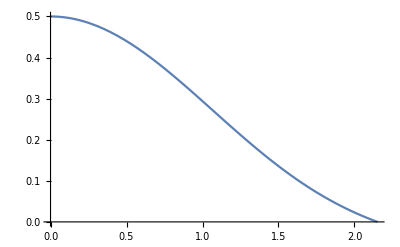

```mathematica
Plot[ρ[ψ[r]/.sol], {r, ϵ, R}]
```

```mathematica
ADMEnergy=4*π*NIntegrate[x^2*(ρ[ψ[x]/.sol][[1]] + 3*P[ψ[x]/.sol][[1]])*(F[x][[1]]),{x, ϵ, R}];
```

```mathematica
NCount = 4*π*5.12*10^56*NIntegrate[x^2*((ψ[x]/.sol)[[1]])/(√(1-((m[x]/.sol)[[1]])/(2*π*x))), {x, ϵ, R}];
```

```mathematica
NCountTilde = 4*π*5.12*10^56*NIntegrate[x^2*(ρ[ψ[x]/.sol][[1]])/(√(1-((m[x]/.sol)[[1]])/(2*π*x))), {x, ϵ, R}];
```

```mathematica
ρ[Subscript[ψ, 0]]
```

0.5

```mathematica
BarMassToSunRatio = 8.37*10^-58*NCount
```

2.33406

```mathematica
R*8
```

17.2093

```mathematica
M[[1]]*0.4285
```

2.1366

```mathematica
0.4285*ADMEnergy
```

2.25256

```mathematica
BarMassToSunRatio - 0.4285*M[[1]]
```

0.197455

```mathematica
NCount
```

2.7886×10^57

```mathematica
NCountTilde
```

3.05114×10^57